## Wobbling frequency for QTR model

```mathematica
ClearAll["Global`*"]
```

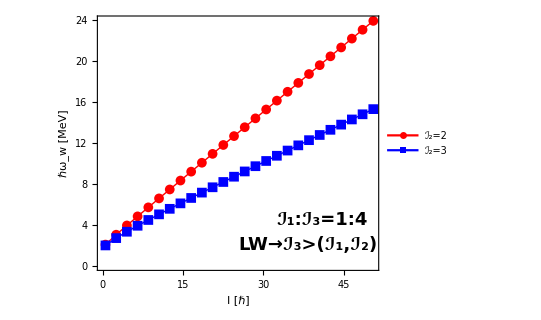

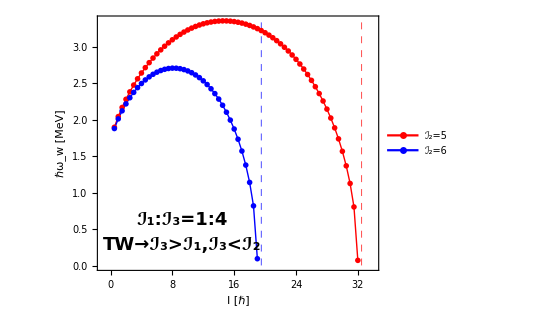

```mathematica
realspin[I_]:=Sqrt[I(I+1)];
omega[I_,j_,I1_,I2_,I3_]:=j/I3 Sqrt[(1+realspin[I]/j(I3/I1-1))(1+realspin[I]/j(I3/I2-1))];
plotdata[j_,I1_,I2_,I3_]:=Table[{spin,omega[spin,j,I1,I2,I3]},{spin,0.5,52,0.5}];
plotdata2[j_,I1_,I2_,I3_]:=Table[{spin,omega[spin,j,I1,I2,I3]},{spin,0.5,52,2}];
fig1=ListPlot[{plotdata2[6.5,1,2,4],plotdata2[6.5,1,3,4]},Joined->True,PlotMarkers->{Automatic, Medium},AspectRatio->0.8,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick},{Blue,Thick}},LabelStyle->{19,Bold,Black,FontFamily->"Arial"},PlotLegends->Placed[{"ℐ_2=2","ℐ_2=3"},{0.2,0.8}],Epilog->{ Inset[Style["ℐ_1:ℐ_3=1:4",Bold,Black,FontFamily->"Arial",18],Scaled[{0.8,0.2}]],Inset[Style["LW→ℐ_3>(ℐ_1,ℐ_2)",Bold,Black,FontFamily->"Arial",18],Scaled[{0.75,0.1}]]},FrameLabel->{"I [ℏ]","ℏω_w [MeV]"},ImageSize->400];
fig2=ListPlot[{plotdata[6.5,1,5,4],plotdata[6.5,1,6,4]},Joined->True,PlotMarkers->"OpenMarkers",AspectRatio->0.8,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick},{Blue,Thick}},LabelStyle->{19,Bold,Black,FontFamily->"Arial"},PlotLegends->Placed[{"ℐ_2=5","ℐ_2=6"},{0.25,0.5}],Epilog->{ Inset[Style["ℐ_1:ℐ_3=1:4",Bold,Black,FontFamily->"Arial",18],Scaled[{0.3,0.2}]],Inset[Style["TW→ℐ_3>ℐ_1,ℐ_3<ℐ_2",Bold,Black,FontFamily->"Arial",18],Scaled[{0.3,0.1}]]},FrameLabel->{"I [ℏ]","ℏω_w [MeV]"},ImageSize->400,GridLines->{{{6.5*5/(5-4),Directive[Opacity[1],Red,Dashed,Thick]},{6.5*6/(6-4),Directive[Opacity[1],Blue,Dashed,Thick]}}, None},PlotRange->{{-1,34},Automatic}];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/odd-A-QTR-Model/wobb_freq_oddA-LW.pdf",fig1,ImageResolution->1200];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/odd-A-QTR-Model/wobb_freq_oddA-TW.pdf",fig2,ImageResolution->1200];
Show[fig1]
Show[fig2]
```

```mathematica
omegaF[x_]:=a1*Sqrt[(1+b1*x)(1+b2*x)];
D[omegaF[x],x]
```

(a1 (b2 (1+b1 x)+b1 (1+b2 x)))/(2 √((1+b1 x) (1+b2 x)))

```mathematica
Solve[D[omegaF[x],x]==0,x]
```

{{x→(-b1-b2)/(2 b1 b2)}}

```mathematica
omegaF[(-b1-b2)/(2 b1 b2)]
```

a1 √((1+(-b1-b2)/(2 b1)) (1+(-b1-b2)/(2 b2)))

```mathematica
b1[j_,I1_,I3_]:=1/j(I3/I1-1);
b2[j_,I2_,I3_]:=1/j(I3/I2-1);
a[j_,I3_]:=j/I3;
```

```mathematica
omegaF[(-b1-b2)/(2 b1 b2)]/.{a1->a[6.5,4],b1->b1[6.5,1,4],b2->b2[6.5,5,4]}
omegaF[(-b1-b2)/(2 b1 b2)]/.{a1->a[6.5,4],b1->b1[6.5,1,4],b2->b2[6.5,6,4]}
```

3.35659

2.70833